## Loading FC and FA

```mathematica
Quit[]
```

```mathematica
$LoadFeynArts=True;
<<FeynCalc`FeynCalc`;
```

FeynCalc 9.2.0. For help, use the documentation center, check out the wiki or write to the mailing list.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput. Phys. Commun., 207C, 432-444, 2016, arXiv:1601.01167

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun., 64, 345-359, 1991.

FeynArts 3.1 patched for use with FeynCalc, for documentation use the manual or visit www.feynarts.de.

## 1. Partonic Calculation

### Imputs

```mathematica
SetOptions[{Plot,LogPlot,LogLogPlot,ListPlot,ListLogLogPlot},ImageSize->600,AspectRatio->0.7,Frame->True,FrameStyle->15,PlotStyle->{Thick},GridLines->Full];
SetOptions[{ListContourPlot},ImageSize->600,AspectRatio->0.7,Frame->True,FrameStyle->15,ContourLabels->True]; (*Plot with frames*)

Clear[mz,e,θw,Mll];
$Assumptions={InM>0,mz>0,M>0};
FCClearScalarProducts[];

Definitions;

Sw=Sin[θw];Cw=Cos[θw];
g=e/Sw;
PL=ChiralityProjector[-1];PR=ChiralityProjector[+1];

cV[x_]:= Switch[x,ν,1/2,l,-1/2+2 Sw^2,u,1/2-4/3 Sw^2,d,-1/2+2/3 Sw^2];
cA[x_]:=Switch[x,ν,1/2,l,-1/2,u,1/2,d,-1/2];
Q[x_]:=Switch[x,ν,0,l,-1,u,2/3,d,-1/3];
MassReplace[x_]:=x/.{mw->80.385,mz->91.1876,Γz->2.4952, e->√(4π 1/127.91),θw->ArcSin[√0.23129]};

Couplings;

gz[q_,μ_]:=ⅈ g/(2Cw)GA[μ].((cV[q])-(cA[q])GA[5]);
gγ[q_,μ_]:=ⅈ Q[q]e GA[μ];
gw[μ_]:=ⅈ g/(√2) GA[μ]. PL;

lProp[p_,m_]:=(ⅈ(FV[p,α]GA[α]+m))/(SP[p]-m^2)//DiracSimplify;
ScalarProp[p_,m_]:=ⅈ/(SP[p]-m^2);
γProp[p_,x_,y_]:=(-ⅈ MT[x,y]/SP[p]);
zProp[p_,x_,y_,flag_]:=( -ⅈ/(SP[p]-mz^2+ⅈ Γz mz))(MT[x,y]-flag(FV[p,x]FV[p,y])/SP[p]); (*Flag=0 to exclude second part*)
wProp[p_,x_,y_,flag_]:=( -ⅈ/(SP[p]-mw^2))(MT[x,y]-flag(FV[p,x]FV[p,y])/SP[p]);
RelFermDiagramSign=-1;

Kinematics;

SP[p1,p1]=mw^2; SP[p2,p2]=0; SP[p3,p3]=0;
SP[p2+p3]=mw^2;
SP[p1,p2]=mw^2/2;SP[p1,p3]=mw^2/2;
SP[p2,p3]=mw^2/2;
mp2=mp3=0;
```

### SM Amplitudes

```mathematica
Amplitudes;

udCurrent[μ_]:= SpinorUBar[p2,mp2].gw[μ].SpinorV[p3,mp3]//DiracSimplify;

AmpW=1/ⅈ udCurrent[μ].PolarizationVector[p1,μ];

AmpliTude SQuare;

AmpSqW=FermionSpinSum[(AmpW)*ComplexConjugate[(AmpW)/.{ μ->ρ}]]/.DiracTrace->Tr //Contract //Simplify;
```

#### Calculating CrossSection

```mathematica
Physical PolarizatioN;

Momp2=mw/2{1,Sθ,0,Cθ};
Momp3=mw/2{1,-Sθ,0,-Cθ};
Eps1p =-1/(√2){0,1,-ⅈ,0};
Eps1m=-1/(√2){0,1,ⅈ,0};
Eps1l=1/mw{0,0,0,-mw};

Pair[{a_,b_,c_,d_},{e_,f_,g_,h_}]:=a e-b f-c g-d h;

ϵ=LeviCivitaTensor[4];
ϵCont[x_,pol_]:=Module[{α1,α2,α3,α4,x1},
x1=x//InputForm;
x1=x1/.{Momentum[p2]->Momp2,Momentum[p3]->Momp3,
Momentum[Polarization[p1,-I]]-> Conjugate[pol],Momentum[Polarization[p1,I]]-> pol};
x1/.{Eps[p1_,p2_,p3_,p4_]:> Sum[p1[[α1]]p2[[α2]]p3[[α3]]p4[[α4]]ϵ[[α1,α2,α3,α4]],{α1,1,4},{α2,1,4},{α3,1,4},{α4,1,4}]}]

AmpSqWTp=ϵCont[AmpSqW,Eps1p]/.{Conjugate[Cθ]->Cθ, Conjugate[Sθ]->Sθ}/.{Sθ->√(1-Cθ^2) ,(e^2*mw^2*Csc[θw]^2)->1}//Simplify;
AmpSqWTn=ϵCont[AmpSqW,Eps1m]/.{Conjugate[Cθ]->Cθ, Conjugate[Sθ]->Sθ}/.{Sθ->√(1-Cθ^2) ,(e^2*mw^2*Csc[θw]^2)->1}//Simplify;
AmpSqWL=ϵCont[AmpSqW,Eps1l]/.{Conjugate[Cθ]->Cθ, Conjugate[Sθ]->Sθ}/.{Sθ->√(1-Cθ^2) ,(e^2*mw^2*Csc[θw]^2)->1}//Simplify;
```

```mathematica
Print[AmpSqWTp]
Print[AmpSqWTn]
Print[AmpSqWL]
```

((-1 + Cθ)^2*e^2*mw^2*Csc[θw]^2)/4

((1 + Cθ)^2*e^2*mw^2*Csc[θw]^2)/4

-((-1 + Cθ^2)*e^2*mw^2*Csc[θw]^2)/2

```mathematica
AmpSqWTp=((-1 + Cθ)^2*e^2*mw^2*Csc[θw]^2)/4/.{(e^2*mw^2*Csc[θw]^2)->1};
AmpSqWTn=((1 + Cθ)^2*e^2*mw^2*Csc[θw]^2)/4/.{(e^2*mw^2*Csc[θw]^2)->1};
AmpSqWL=-((-1 + Cθ^2)*e^2*mw^2*Csc[θw]^2)/2/.{(e^2*mw^2*Csc[θw]^2)->1};
```

```mathematica
Print[AmpSqWTp]
Print[AmpSqWTn]
Print[AmpSqWL]
```

1/4 (Cθ-1)^2

1/4 (Cθ+1)^2

1/2 (1-Cθ^2)

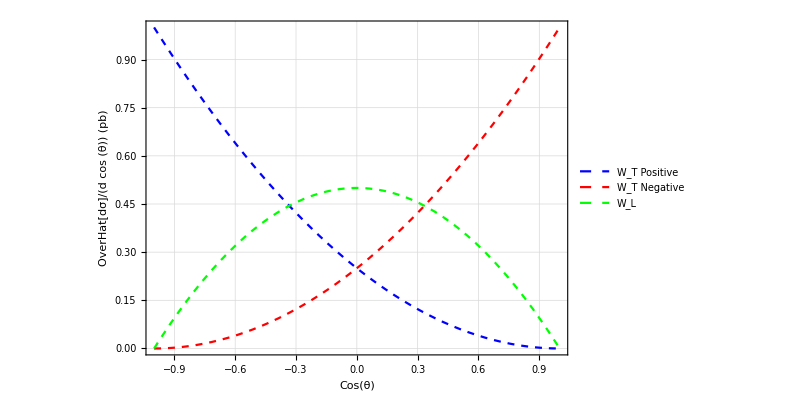

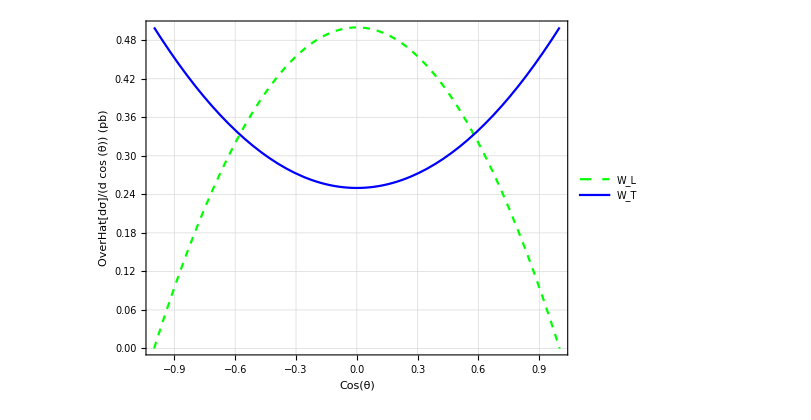

```mathematica
AmpSqWTpPlot=Plot[AmpSqWTp ,{Cθ,-1,1},PlotStyle->{Dashed,Blue},PlotLegends->{"W_T Positive"},PlotRange->All,FrameLabel->{"Cos(θ)",Rotate[Style["OverHat[dσ]/(d cos (θ)) (pb)"],-90Degree],"W decay - Parton Level"}];
AmpSqWTnPlot=Plot[AmpSqWTn ,{Cθ,-1,1},PlotStyle->{Dashed,Red},PlotLegends->{"W_T Negative"},PlotRange->All,FrameLabel->{"Cos(θ)",Rotate[Style["OverHat[dσ]/(d cos (θ)) (pb)"],-90Degree],"W decay - Parton Level"}];
AmpSqWLPlot=Plot[AmpSqWL,{Cθ,-1,1},PlotStyle->{Dashed,Green},PlotLegends->{"W_L"},PlotRange->All,FrameLabel->{"Cos(θ)",Rotate[Style["OverHat[dσ]/(d cos (θ)) (pb)"],-90Degree],"W decay - Parton Level"}];
AmpSqWTPlot=Plot[1/2(AmpSqWTp+AmpSqWTn),{Cθ,-1,1},PlotStyle->{Blue},PlotLegends->{"W_T"},PlotRange->All,FrameLabel->{"Cos(θ)",Rotate[Style["OverHat[dσ]/(d cos (θ)) (pb)"],-90Degree],"W decay - Parton Level"}];
Show[AmpSqWTpPlot,AmpSqWTnPlot,AmpSqWLPlot]
Show[AmpSqWLPlot,AmpSqWTPlot]
```

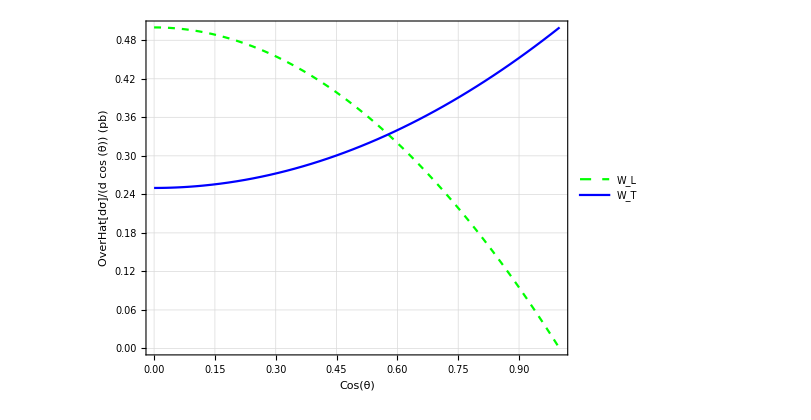

```mathematica
AmpSqWLPlot2=Plot[AmpSqWL,{Cθ,0,1},PlotStyle->{Dashed,Green},PlotLegends->{"W_L"},PlotRange->All,FrameLabel->{"Cos(θ)",Rotate[Style["OverHat[dσ]/(d cos (θ)) (pb)"],-90Degree],"W decay - Parton Level"}];
AmpSqWTPlot2=Plot[1/2(AmpSqWTp+AmpSqWTn),{Cθ,0,1},PlotStyle->{Blue},PlotLegends->{"W_T"},PlotRange->All,FrameLabel->{"Cos(θ)",Rotate[Style["OverHat[dσ]/(d cos (θ)) (pb)"],-90Degree],"W decay - Parton Level"}];
Show[AmpSqWLPlot2,AmpSqWTPlot2]
```